# Presentation Plots

18/02/2021 - Cory Aitchison

## Simple RLC circuits (with shunt capacitors)

```mathematica
ClearAll;
Off[FindMinimum::sszero]
Clear[ω, Z, Imp, Γ, S11, fres, L, Cp, R, Cs];
Z0 = 50;
ω[f_] := 2*Pi*f;
Z[L_, R_, Cp_, Cs_, f_] := ((I ω[f] L + 1/(1/R + I ω[f] Cp))^-1 + I ω[f] Cs)^-1;
Γ[L_,R_,Cp_,Cs_,f_] := (Z[L,R,Cp,Cs,f] - Z0) / (Z[L,R,Cp,Cs,f] + Z0);
S11[L_,R_,Cp_,Cs_,f_] := Abs[Γ[L,R,Cp,Cs,f]]^2;
Phase[L_,R_,Cp_,Cs_,f_] := Arg[Γ[L,R,Cp,Cs,f]];
Fres[L_,R_,Cp_,Cs_] := Abs[f /. Last[FindMinimum[S11[L,R,Cp,Cs,f*1*^7],{f,5}]]] * 1*^7;
L =390*^-9;
Cp = 26*^-12;
R = 1000;
Cs = 0*^-12;
fff =Fres[L,R,Cp,Cs];
```

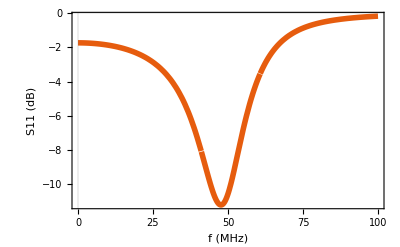

```mathematica
Plot[20*Log10@S11[L,R,Cp,0,f*1*^6], {f,0, 100}, PlotRange->All,PlotTheme->"Scientific", FrameLabel->{Style["f (MHz)",FontSlant->Italic], Style["S11 (dB)",FontSlant->Italic]},LabelStyle->{FontSize-> 20, FontFamily-> "Times", FontColor-> Black}, PlotStyle->Thickness[0.01], ImageSize->400]
```

```mathematica
Export["/Users/caitchison/Google Drive/Undergrad/SQA/Report/images/S11_resonance.pdf", %298];
```

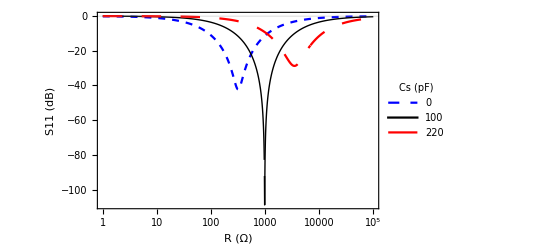

```mathematica
LogLinearPlot[{20*Log10@S11[L,R,Cp,0,Fres[L,1000,Cp,0]],20*Log10@S11[L,R,Cp,100*^-12,Fres[L,1000,Cp,100*^-12]],20*Log10@S11[L,R,Cp,220*^-12,Fres[L,1000,Cp,220*^-12]]},{R,10^0,10^5},PlotRange->All, PlotStyle->{{Blue, Dashed}, {Black, Thick}, {Red, Dashing[Large]}}, PlotLegends->Placed[LineLegend[{"0", "100", "220"}, LegendLabel->"Cs (pF)"],{0.3,0.4}], PlotTheme->"Scientific", FrameLabel->{Style["R (Ω)",FontSlant->Italic], Style["S11 (dB)",FontSlant->Italic]},LabelStyle->{FontSize-> 20, FontFamily-> "Times", FontColor-> Black}, PlotStyle->Thickness[0.01], ImageSize->400]
```

```mathematica
Export["/Users/caitchison/Google Drive/Undergrad/SQA/Report/images/cs_comparison.pdf", %435];
```

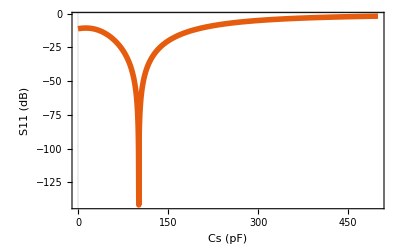

```mathematica
Plot[20*Log10@S11[L,R,Cp,Cs*1*^-12, Fres[L,R,Cp,Cs*1*^-12]],{Cs, 0, 500},PlotRange->All, PlotTheme->"Scientific", FrameLabel->{Style["Cs (pF)",FontSlant->Italic], Style["S11 (dB)",FontSlant->Italic]},LabelStyle->{FontSize-> 20, FontFamily-> "Times", FontColor-> Black}, PlotStyle->Thickness[0.01], ImageSize->400]
```

```mathematica
Export["/Users/caitchison/Google Drive/Undergrad/SQA/Report/images/cs_simulation.pdf", %289];
```

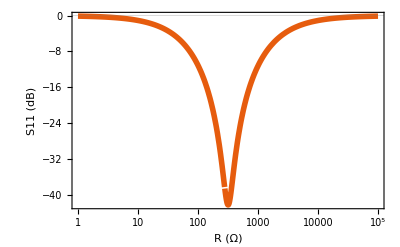

```mathematica
Cs = 0;
LogLinearPlot[20*Log10@S11[L,R,Cp,Cs,fff],{R,10^0,10^5},PlotRange->All, PlotTheme->"Scientific", FrameLabel->{Style["R (Ω)",FontSlant->Italic], Style["S11 (dB)",FontSlant->Italic]},LabelStyle->{FontSize-> 20, FontFamily-> "Times", FontColor-> Black}, PlotStyle->Thickness[0.01], ImageSize->400]
```

```mathematica
Export["/Users/caitchison/Google Drive/Undergrad/SQA/Report/images/S11_cs0db.pdf", %302];
```

## “Improved” function (not really)

```mathematica
(*ClearAll*)
Off[FindMinimum::sszero]
(*Clear[ω, Z, Imp, Γ, S11, fres, L, Cp, R, Cs]*)
Z0 = 50;
ω[f_] := 2*Pi*f;
(*Z[L_, R_, Cp_, Cs_, f_] := ((I ω[f] L + 1/(1/R + I ω[f] Cp))^-1 + I ω[f] Cs)^-1;*)
C6 = 22*^-12;
C7 = 1;
C10 = 100*^-12;
CLF = 1*^-9;
CBT = 22*^-9;
Zb[L_,R_,Cp_,Cs_,f_]:= 1/(I ω[f] CBT) + 1/(I ω[f] C10) + 1/(I ω[f] C6) + 1/((I ω[f] L + 1/(1/(R+1/(I ω[f] CLF)) + I ω[f] Cp))^-1 + I ω[f] Cs);
Γb[L_,R_,Cp_,Cs_,f_] := (Zb[L,R,Cp,Cs,f] - Z0) / (Zb[L,R,Cp,Cs,f] + Z0);
S11b[L_,R_,Cp_,Cs_,f_] := Abs[Γb[L,R,Cp,Cs,f]]^2;
Phase[L_,R_,Cp_,Cs_,f_] := Arg[Γ[L,R,Cp,Cs,f]];
Fresb[L_,R_,Cp_,Cs_] := Abs[f /. Last[FindMinimum[S11b[L,R,Cp,Cs,f*1*^7],{f,5}]]] * 1*^7;
```

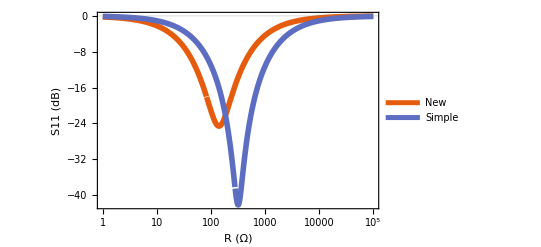

```mathematica
L = 390*^-9;
R = 1000;
Cp = 26*^-12;
Cs = 0*^-12;
fffb = Fresb[L,R,Cp,Cs];
LogLinearPlot[{20*Log10@S11b[L,R,Cp,Cs,fffb],20*Log10@S11[L,R,Cp,Cs,fff]},{R,10^0,10^5},PlotRange->All,  PlotTheme->"Scientific", FrameLabel->{Style["R (Ω)",FontSlant->Italic], Style["S11 (dB)",FontSlant->Italic]},LabelStyle->{FontSize-> 20, FontFamily-> "Times", FontColor-> Black}, PlotStyle->Thickness[0.01], ImageSize->400, PlotLegends->Placed[LineLegend[{"New", "Simple"}],{0.2,0.2}]]
```

```mathematica
Export["/Users/caitchison/Google Drive/Undergrad/SQA/Report/images/transfer_improved.pdf", %429];
```

## Why it didn’t work?

15.216

323.184

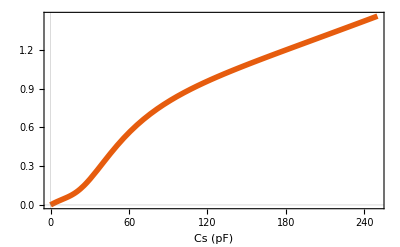

```mathematica
Cs = 10*^-12;
Cp = 26*^-12;
Abs[Z[L,R,Cp,Cs, Fres[L,R,Cp,Cs]]]
1/(ω[Fres[L,R,Cp,Cs]]*Cs)
Plot[(ω[Fres[L,R,Cp,Cs*1*^-12]]* Cs*1*^-12) *Abs[Z[L,R,Cp,0, Fres[L,R,Cp,Cs*1*^-12]]], {Cs, 0, 250}, PlotTheme->"Scientific", FrameLabel->{Style["Cs (pF)",FontSlant->Italic], Style["",FontSlant->Italic]},LabelStyle->{FontSize-> 20, FontFamily-> "Times", FontColor-> Black}, PlotStyle->Thickness[0.01], ImageSize->400]
```

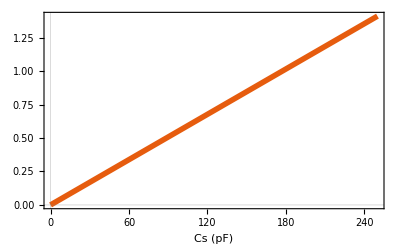

```mathematica
Cs = 10*^-12;
Cp = 26*^-12;
R = 1000;
ffff=Fres[L,R,Cp,0];
Plot[(ω[ffff]* Cs*1*^-12 )*Abs[Z[L,R,Cp,0,ffff]], {Cs, 0, 250}, PlotTheme->"Scientific", FrameLabel->{Style["Cs (pF)",FontSlant->Italic], Style["",FontSlant->Italic]},LabelStyle->{FontSize-> 20, FontFamily-> "Times", FontColor-> Black}, PlotStyle->Thickness[0.01], ImageSize->400]
```

```mathematica
Export["/Users/caitchison/Google Drive/Undergrad/SQA/Report/images/impedanceratio.pdf", %188];
```